```mathematica
data={{-1,-1},{-1,1},{-2,1},{2,2},{3,2},{3,-1},{3,-2},{-1,-1}}
```

{{-1,-1},{-1,1},{-2,1},{2,2},{3,2},{3,-1},{3,-2},{-1,-1}}

```mathematica
x=Transpose[data][[1]] (* not included in 2025 *)
```

{-1,-1,-2,2,3,3,3,-1}

```mathematica
y=Transpose[data][[2]] (* not included in 2025 *)
```

{-1,1,1,2,2,-1,-2,-1}

```mathematica
sx=Interpolation[x] (* not included in 2025 *)
```

InterpolatingFunction[…]

```mathematica
sy=Interpolation[y] (* not included in 2025 *)
```

InterpolatingFunction[…]

```mathematica
sp[t_]:={sx[t],sy[t]}
```

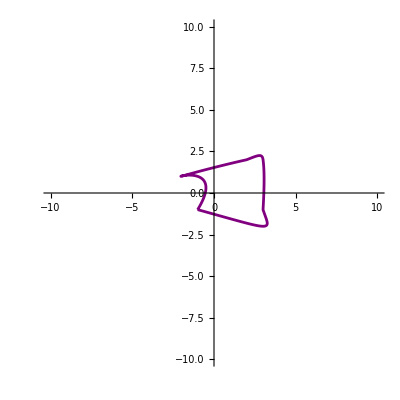

```mathematica
ParametricPlot[sp[t],{t,1,Length[x]},PlotStyle->Purple,PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
trx[s_]:=s*Cos[s]
```

```mathematica
try[s_]:=s*Sin[s]
```

```mathematica
tr[s_]:={trx[s],try[s]}
```

```mathematica
Traj:=ParametricPlot[tr[s],{s,0,10},PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
MovSpl[s_,color_]:=ParametricPlot[sp[t]+tr[s],{t,1,Length[x]},PlotStyle->color,PlotRange->{{-10,10},{-10,10}}]
```

```mathematica
S[s_,color_]:=Show[MovSpl[s,color],Traj]
```

```mathematica
mySlider={Slider[Dynamic[s],{0,10,1}],Dynamic[s]}
```

{,}

```mathematica
C1={Black,Red,Green,Blue,Orange}
```

{GrayLevel[0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0]}

```mathematica
myBar=SetterBar[Dynamic[color],C1]
```

|  |  |  |

```mathematica
{Dynamic[S[s,color]],mySlider,myBar}
```

{,{,}, |  |  |  | }